```mathematica
a
```

a

```mathematica
usbcs={"adcirc_flow","adcirc_stage","rdhm_flow"};
dsbcs={"adcirc_stage","stage_0"};
sites={"greenville","rock_springs","grimesland"};
```

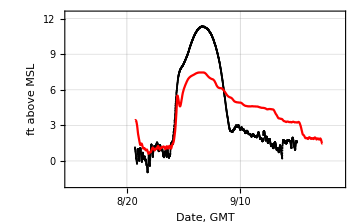

```mathematica
eventname="irene";
r=StringJoin["C:\\Users\\Sam\\Dropbox\\",eventname];


hecplot["irene","adcirc_flow","adcirc_stage","greenville","stage"]
```

# Greenville

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-432, na], Max[12801, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

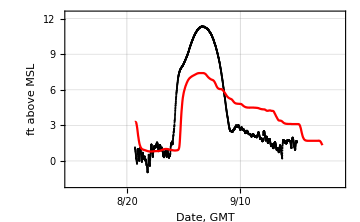
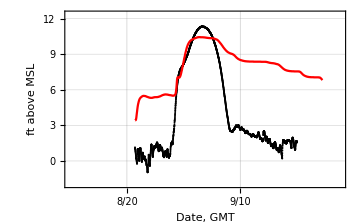
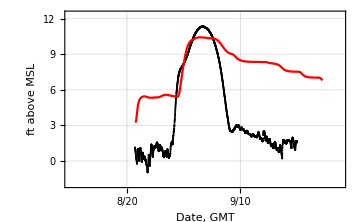
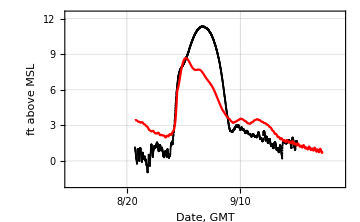
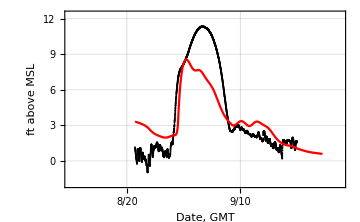
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

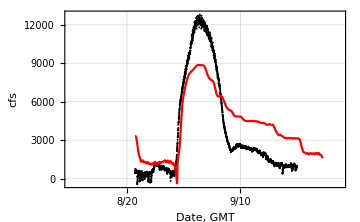
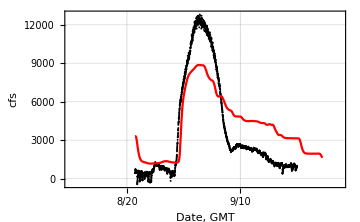
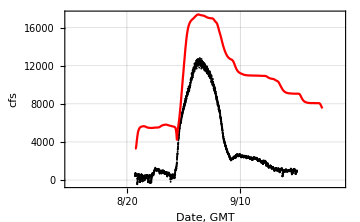
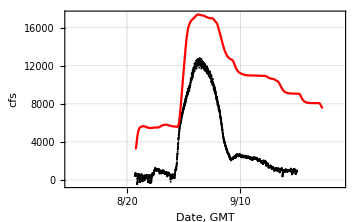
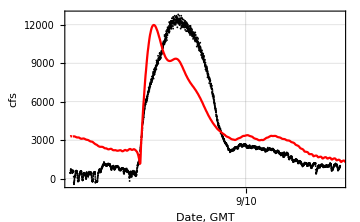
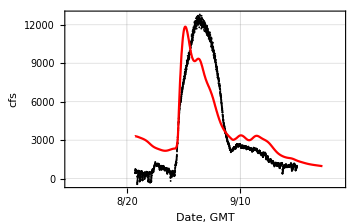
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="greenville";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
flowplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"flow"];
Export[StringJoin[r,"\\",sitename,"_flow_with_US",usname,"_DS",dsname,".eps"],flowplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_flow_with_US",usname,"_DS",dsname,".wmf"],flowplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
flowplots//MatrixForm
```

```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

{{□,□,□,□},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-}}

```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

{{□,□,□,□},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-}}

# Rock Springs

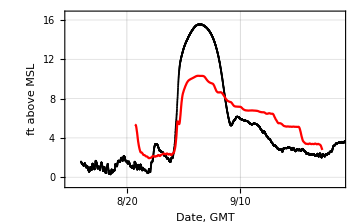
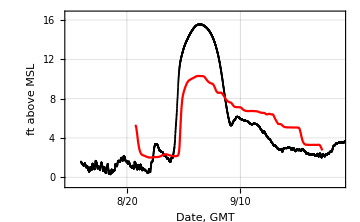
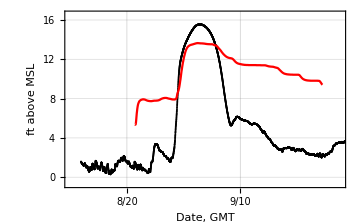
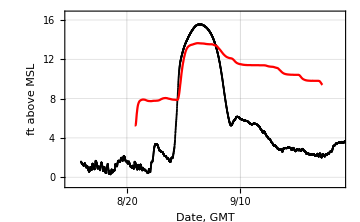
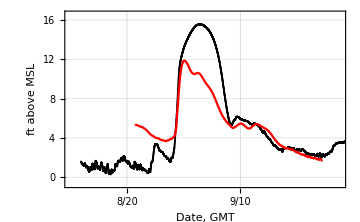
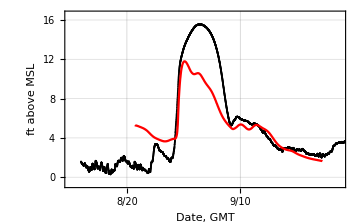
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="rock_springs";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

{{□,□,□,□},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-}}

# Grimesland

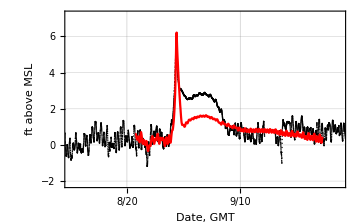
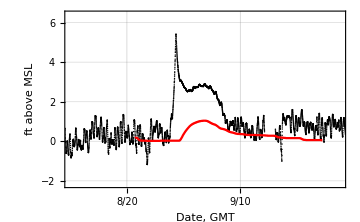
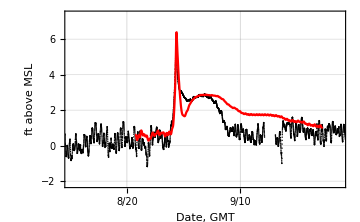
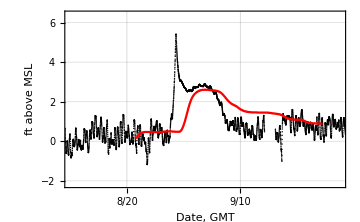
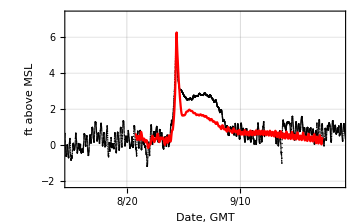
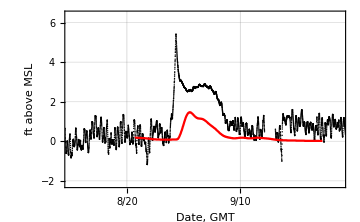
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="grimesland";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

```mathematica
({{□, □, □, □}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}, {□, □, -Graphics-, -Graphics-}})
```

{{□,□,□,□},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-},{□,□,-Graphics-,-Graphics-}}

## Pamlico at Washington

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-1.14, na], Max[29.24, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[0, na], Max[29.24, 1 + na]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

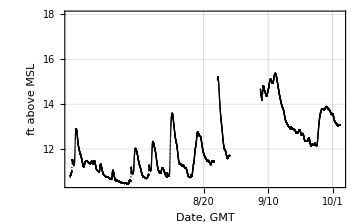
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="24100";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".eps"],stageplots[[i,j]]];
Export[StringJoin[r,"\\",sitename,"_stage_with_US",usname,"_DS",dsname,".wmf"],stageplots[[i,j]]];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

Part::partw: Part 1 of {} does not exist.

ToExpression::notstrbox: {} ⟦ 1 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 2 of {} does not exist.

ToExpression::notstrbox: {} ⟦ 2 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Transpose::nmtx: The first two levels of {86400\ $Failed, $Failed} cannot be transposed.

ToExpression::notstrbox: Transpose[{86400\ $Failed, $Failed}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-0.36, $Failed], Max[8, 1 + $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-0.36, $Failed], Max[8, 1 + $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-0.36, $Failed], Max[8, 1 + $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {86400\ $Failed, $Failed} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

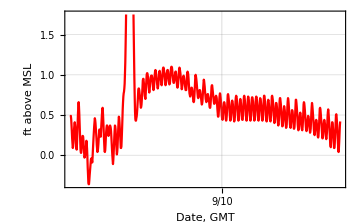
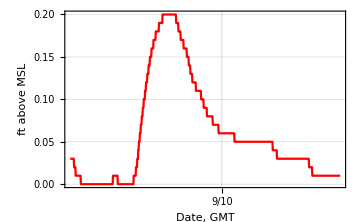
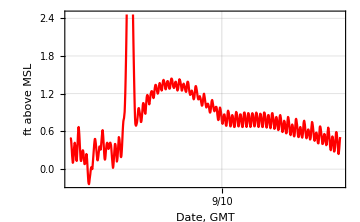
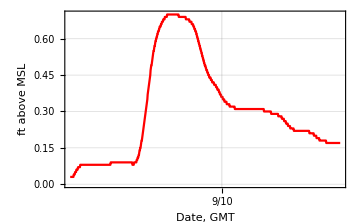
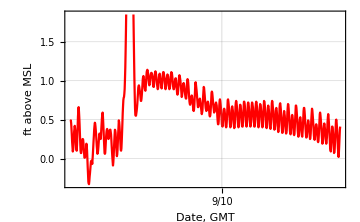
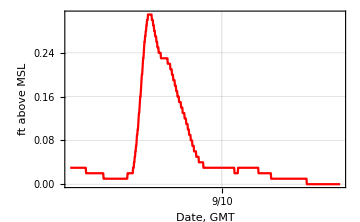
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="25100";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```

Part::partw: Part 1 of {} does not exist.

ToExpression::notstrbox: {} ⟦ 1 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Part::partw: Part 2 of {} does not exist.

ToExpression::notstrbox: {} ⟦ 2 ⟧ is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

Transpose::nmtx: The first two levels of {86400\ $Failed, $Failed} cannot be transposed.

ToExpression::notstrbox: Transpose[{86400\ $Failed, $Failed}] is not a string or a box. ToExpression can only interpret strings or boxes as Wolfram Language input.

General::stop: Further output of ToExpression :: notstrbox will be suppressed during this calculation.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-0.36, $Failed], Max[7.76, 1 + $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-0.36, $Failed], Max[7.76, 1 + $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

ListPlot::prng: Value of option PlotRange -> {{3521923200, 3526243200}, {-1 + Min[-0.36, $Failed], Max[7.76, 1 + $Failed]}} is not All, Full, Automatic, a positive machine number, or an appropriate list of range specifications.

General::stop: Further output of ListPlot :: prng will be suppressed during this calculation.

ListPlot::lpn: $Failed is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot :: lpn will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Transpose::nmtx: The first two levels of {86400\ $Failed, $Failed} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

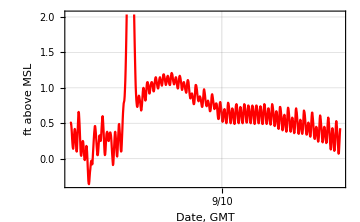
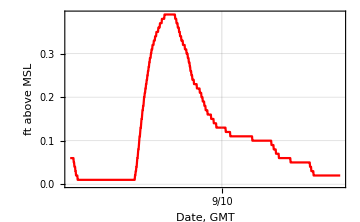
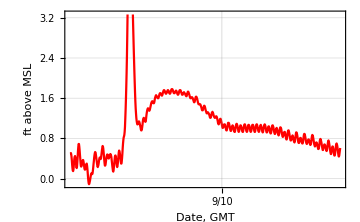
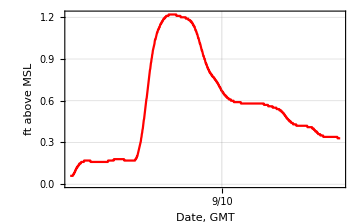
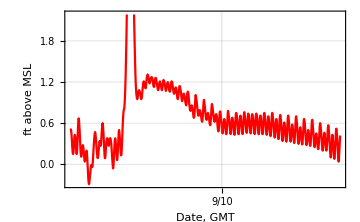
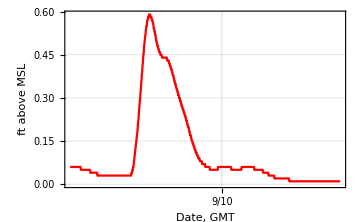
(-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
-Graphics- | -Graphics- | 0 | 0
0 | 0 | 0 | 0)

```mathematica
sitename="26100";
plots=Table[0,{4}];
plots=Table[plots,{4}];
stageplots=plots;
flowplots=plots;

Do[
usname=usbcs[[i]];
Do[
dsname=dsbcs[[j]];
stageplots[[i,j]]=hecplot[eventname,usname,dsname,sitename,"stage"];
,{j,1,2}];
,{i,1,3}];

stageplots//MatrixForm
```